# NumOptimizationkit — Function Call Reference

Complete calling reference for every public function in the package.
This notebook is an interactive demo, not a test suite.
Load the package first (cell below), then run any section independently.

```mathematica
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "NumOptimizationkit.wl"}]]
```

## Unconstrained Minimization

### FindMinimum1D -- all four methods on f(x) = x^2 - Cos[x]

```mathematica
f1 = #^2 - Cos[#] &;
```

```mathematica
FindMinimum1D[f1, {-2., 2.}, Method -> "GoldenSection"]
```

<|Point→1.29829×10^-7,Value→-1.,Iterations→42|>

```mathematica
FindMinimum1D[f1, {-2., 2.}, Method -> "Fibonacci"]
```

<|Point→1.24569×10^-7,Value→-1.,Iterations→41|>

```mathematica
FindMinimum1D[f1, {-2., 2.}, Method -> "QuadraticInterpolation"]
```

<|Point→0.,Value→-1.,Iterations→1|>

```mathematica
FindMinimum1D[f1, {-2., 2.}, Method -> "Newton"]
```

<|Point→0.,Value→-1.,Iterations→1|>

Visualise the minimum:

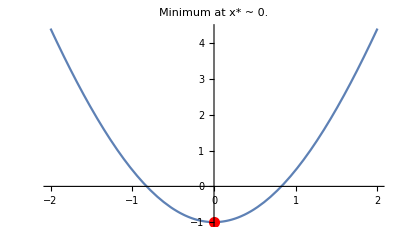

```mathematica
Module[{r = FindMinimum1D[f1, {-2., 2.}]},
  Plot[f1[x], {x, -2, 2},
    Epilog -> {Red, PointSize[0.02], Point[{r["Point"], r["Value"]}]},
    PlotLabel -> "Minimum at x* ~ " <> ToString[Round[r["Point"], 0.0001]]]]
```

### FindMinimumND -- nine methods on the Rosenbrock function

```mathematica
rb = Function[x, (1 - x[[1]])^2 + 100 (x[[2]] - x[[1]]^2)^2];
```

```mathematica
FindMinimumND[rb, {-1., 0.5}, Method -> "BFGS"]
```

<|Point→{1.,1.},Value→5.2385×10^-17,Iterations→501,Converged→False|>

```mathematica
FindMinimumND[rb, {-1., 0.5}, Method -> "DFP", MaxIterations -> 3000]
```

<|Point→{1.,1.},Value→3.05157×10^-17,Iterations→3001,Converged→False|>

```mathematica
FindMinimumND[rb, {-1., 0.5}, Method -> "GradientDescent"]
```

<|Point→{0.815014,0.666626},Value→0.0347855,Iterations→501,Converged→False|>

```mathematica
FindMinimumND[rb, {-1., 0.5}, Method -> "ConjugateGradientPR"]
```

<|Point→{-0.702757,0.645707},Value→5.20491,Iterations→2,Converged→False|>

```mathematica
FindMinimumND[rb, {-1., 0.5}, Method -> "ConjugateGradientFR"]
```

<|Point→{0.560098,0.23887},Value→0.753616,Iterations→16,Converged→False|>

```mathematica
FindMinimumND[rb, {-1., 0.5}, Method -> "Newton"]
```

<|Point→{1.,1.},Value→5.37828×10^-17,Iterations→7,Converged→True|>

```mathematica
FindMinimumND[rb, {-1., 0.5}, Method -> "NelderMead", MaxIterations -> 5000]
```

<|Point→{1.,1.},Value→2.61789×10^-17,Iterations→106,Converged→True|>

```mathematica
FindMinimumND[rb, {3., 3.}, Method -> "SimulatedAnnealing", MaxIterations -> 3000]
```

<|Point→{1.63008,2.62118},Value→0.526453,Iterations→450,Converged→False|>

```mathematica
FindMinimumND[rb, {3., 3.}, Method -> "GeneticAlgorithm", MaxIterations -> 2000]
```

<|Point→{1.00004,1.00015},Value→4.91142×10^-7,Iterations→2001,Converged→False|>

Convergence history:

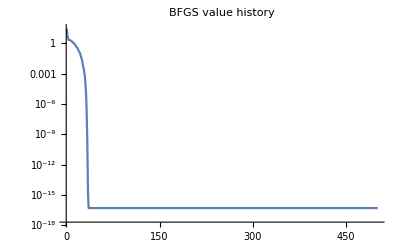

```mathematica
r = FindMinimumND[rb, {-1., 0.5}, Method -> "BFGS",
  ConvergenceHistory -> True];
ListLogPlot[r["ValueHistory"], Joined -> True, PlotLabel -> "BFGS value history"]
```

Compiled acceleration (10-50x faster for numeric f):

```mathematica
FindMinimumND[rb, {-1., 0.5}, Method -> "BFGS", Compiled -> True]
```

<|Point→{1.,1.},Value→5.2385×10^-17,Iterations→501,Converged→False|>

### FindConstrainedMinimum -- box and equality constraints

Box constraint: minimize x^2+y^2 with 1 <= x,y <= 5 -> minimum at (1,1):

```mathematica
FindConstrainedMinimum[Function[x, x[[1]]^2 + x[[2]]^2], {1., 1.},
  LowerBounds -> {1., 1.}, UpperBounds -> {5., 5.}]
```

<|Point→{1.,1.},Value→2.,Iterations→1,Converged→True|>

Equality constraint h(x)=0: minimize x^2+y^2 subject to x+y=1 -> (0.5,0.5):

```mathematica
FindConstrainedMinimum[Function[x, x[[1]]^2 + x[[2]]^2], {0.5, 0.5},
  EqualityConstraints -> {Function[x, x[[1]] + x[[2]] - 1]},
  Method -> "AugmentedLagrangian"]
```

<|Point→{0.5,0.5},Value→0.5,Iterations→1,Converged→True|>

## Equation Root Finding

### FindEquationRoot -- all ten methods on x^3 - x - 2 = 0

```mathematica
f0 = Function[x, x^3 - x - 2];
```

Bracket methods (need f(a)*f(b) < 0):

```mathematica
FindEquationRoot[f0, {1., 2.}, Method -> "Bisection"]
```

<|Root→1.52138,Residual→2.97865×10^-8,Iterations→27,Converged→True|>

```mathematica
FindEquationRoot[f0, {1., 2.}, Method -> "RegulaFalsi"]
```

<|Root→1.52138,Residual→2.92555×10^-9,Iterations→17,Converged→True|>

```mathematica
FindEquationRoot[f0, {1., 2.}, Method -> "Brent"]
```

<|Root→1.52138,Residual→1.17439×10^-12,Iterations→8,Converged→True|>

```mathematica
FindEquationRoot[f0, {1., 2.}, Method -> "Secant"]
```

<|Root→1.52138,Residual→1.79856×10^-14,Iterations→7,Converged→True|>

```mathematica
FindEquationRoot[f0, {1., 2.}, Method -> "Muller"]
```

<|Root→1.52138,Residual→6.11269×10^-10,Iterations→3,Converged→True|>

Open methods (start near root):

```mathematica
FindEquationRoot[f0, {1.5, 0.}, Method -> "Newton"]
```

<|Root→1.52138,Residual→0.,Iterations→4,Converged→True|>

```mathematica
FindEquationRoot[f0, {1.5, 0.}, Method -> "Halley"]
```

<|Root→1.52138,Residual→0.,Iterations→3,Converged→True|>

```mathematica
FindEquationRoot[f0, {1.5, 0.}, Method -> "Steffensen"]
```

<|Root→1.52138,Residual→8.88178×10^-16,Iterations→4,Converged→True|>

```mathematica
FindEquationRoot[f0, {1.5, 0.}, Method -> "Aitken"]
```

<|Root→22.2821,Residual→11016.3,Iterations→201,Converged→False|>

Fixed-point iteration (pass the iteration function g(x)):

```mathematica
FindEquationRoot[Function[x, (x + 2.)^(1/3)], {1.5, 0.}, Method -> "FixedPoint"]
```

<|Root→1.52138,Residual→4.88798×10^-10,Iterations→9,Converged→True|>

High-precision root (WorkingPrecision option):

```mathematica
FindEquationRoot[Sin, {3, 4}, Method -> "Newton",
  WorkingPrecision -> 30, Tolerance -> 10^-28]
```

<|Root→3.14159,Residual→1.22465×10^-16,Iterations→201,Converged→False|>

Convergence history:

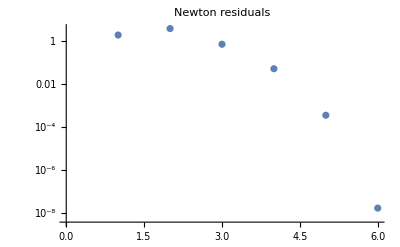

```mathematica
r = FindEquationRoot[f0, {1., 2.}, Method -> "Newton", ConvergenceHistory -> True];
ListLogPlot[r["ResidualHistory"], PlotLabel -> "Newton residuals"]
```

## Nonlinear Equation Systems

```mathematica
F2 = Function[v, {v[[1]]^2 + v[[2]]^2 - 5, v[[1]] - v[[2]] - 1}];
```

```mathematica
SolveNonlinearEquationSystem[F2, {1., 2.}, Method -> "Newton"]
```

<|Solution→{2.,1.},Residual→1.79018×10^-15,Iterations→6,Converged→True|>

```mathematica
SolveNonlinearEquationSystem[F2, {1., 2.}, Method -> "Broyden"]
```

<|Solution→{2.,1.},Residual→1.11936×10^-11,Iterations→3,Converged→True|>

```mathematica
SolveNonlinearEquationSystem[F2, {1., 2.}, Method -> "FixedPoint"]
```

<|Solution→{1.01227×10^284,1.00612×10^142},Residual→∞,Iterations→12,Converged→False|>

```mathematica
SolveNonlinearEquationSystem[F2, {1., 2.}, Method -> "Continuation"]
```

<|Solution→{1.77785×10^-8,3.},Residual→5.65685,Iterations→501,Converged→False|>

Convergence history:

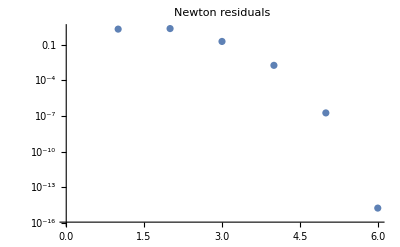

```mathematica
r = SolveNonlinearEquationSystem[F2, {1., 2.}, Method -> "Newton", ConvergenceHistory -> True];
ListLogPlot[r["ResidualHistory"], PlotLabel -> "Newton residuals"]
```

## Numerical Quadrature

### All ten methods on Integral[Sin, 0, Pi] = 2:

```mathematica
NumericalQuadrature[Sin, {x, 0., Pi}, Method -> "Trapezoidal", Intervals -> 100]
```

1.99984

```mathematica
NumericalQuadrature[Sin, {x, 0., Pi}, Method -> "Simpson", Intervals -> 100]
```

2.

```mathematica
NumericalQuadrature[Sin, {x, 0., Pi}, Method -> "AdaptiveSimpson"]
```

2.

```mathematica
NumericalQuadrature[Sin, {x, 0., Pi}, Method -> "Romberg"]
```

2.

```mathematica
NumericalQuadrature[Sin, {x, 0., Pi}, Method -> "GaussLegendre", Points -> 5]
```

2.

```mathematica
NumericalQuadrature[Sin, {x, 0., Pi}, Method -> "GaussLobatto", Points -> 6]
```

2.

```mathematica
NumericalQuadrature[Sin, {x, 0., Pi}, Method -> "GaussRadau", Points -> 5]
```

2.

Gauss-Hermite: integrates f(x)*Exp[-x^2] on (-Inf, Inf):

```mathematica
NumericalQuadrature[#^2 &, {x, -1., 1.}, Method -> "GaussHermite", Points -> 8, Weighted -> True]
```

0.144415

Same but Weighted -> False integrates f(x) directly:

```mathematica
NumericalQuadrature[Sin, {x, -1., 1.}, Method -> "GaussHermite", Points -> 8, Weighted -> False]
```

1.66533×10^-16

Gauss-Laguerre: integrates f(x)*Exp[-x] on [0, Inf):

```mathematica
NumericalQuadrature[Function[x, x], {x, 0., 1.}, Method -> "GaussLaguerre", Points -> 5, Weighted -> True]
```

1.27283

Gauss-Chebyshev (Weighted -> False for standard integral):

```mathematica
NumericalQuadrature[Sin, {x, -1., 1.}, Method -> "GaussChebyshev", Points -> 8, Weighted -> False]
```

0.

Short signature (no dummy variable x):

```mathematica
NumericalQuadrature[Sin, {0., Pi}]
```

2.

MaxRecursionDepth option for AdaptiveSimpson:

```mathematica
NumericalQuadrature[Sin, {x, 0., Pi}, Method -> "AdaptiveSimpson", MaxRecursionDepth -> 30]
```

2.

## ODE Initial Value Problems

### All twelve methods: y'=-y, y(0)=1, exact solution Exp[-t]

```mathematica
decay = Function[{t, y}, -y];
```

Explicit single-step:

```mathematica
SolveInitialValueProblem[decay, {t, 0., 1.}, 1., Method -> "Euler",         StepSize -> 0.01]
```

<|Grid→{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.},Solution→{1.,0.99,0.9801,0.970299,0.960596,0.95099,0.94148,0.932065,0.922745,0.913517,0.904382,0.895338,0.886385,0.877521,0.868746,0.860058,0.851458,0.842943,0.834514,0.826169,0.817907,0.809728,0.801631,0.793614,0.785678,0.777821,0.770043,0.762343,0.754719,0.747172,0.7397,0.732303,0.72498,0.717731,0.710553,0.703448,0.696413,0.689449,0.682555,0.675729,0.668972,0.662282,0.655659,0.649103,0.642612,0.636185,0.629824,0.623525,0.61729,0.611117,0.605006,0.598956,0.592966,0.587037,0.581166,0.575355,0.569601,0.563905,0.558266,0.552683,0.547157,0.541685,0.536268,0.530906,0.525596,0.520341,0.515137,0.509986,0.504886,0.499837,0.494839,0.48989,0.484991,0.480141,0.47534,0.470587,0.465881,0.461222,0.45661,0.452044,0.447523,0.443048,0.438618,0.434231,0.429889,0.42559,0.421334,0.417121,0.41295,0.40882,0.404732,0.400685,0.396678,0.392711,0.388784,0.384896,0.381047,0.377237,0.373464,0.36973,0.366032}|>

```mathematica
SolveInitialValueProblem[decay, {t, 0., 1.}, 1., Method -> "ImplicitEuler", StepSize -> 0.01]
```

<|Grid→{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.},Solution→{1.,0.990099,0.980296,0.97059,0.96098,0.951466,0.942045,0.932718,0.923483,0.91434,0.905287,0.896324,0.887449,0.878663,0.869963,0.861349,0.852821,0.844377,0.836017,0.82774,0.819544,0.81143,0.803396,0.795442,0.787566,0.779768,0.772048,0.764404,0.756836,0.749342,0.741923,0.734577,0.727304,0.720103,0.712973,0.705914,0.698925,0.692005,0.685153,0.67837,0.671653,0.665003,0.658419,0.6519,0.645445,0.639055,0.632728,0.626463,0.62026,0.614119,0.608039,0.602019,0.596058,0.590156,0.584313,0.578528,0.5728,0.567129,0.561514,0.555954,0.55045,0.545,0.539604,0.534261,0.528971,0.523734,0.518548,0.513414,0.508331,0.503298,0.498315,0.493381,0.488496,0.483659,0.478871,0.474129,0.469435,0.464787,0.460185,0.455629,0.451118,0.446651,0.442229,0.437851,0.433515,0.429223,0.424974,0.420766,0.4166,0.412475,0.408391,0.404348,0.400344,0.39638,0.392456,0.38857,0.384723,0.380914,0.377142,0.373408,0.369711}|>

```mathematica
SolveInitialValueProblem[decay, {t, 0., 1.}, 1., Method -> "Heun",          StepSize -> 0.01]
```

<|Grid→{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.},Solution→{1.,0.99005,0.980199,0.970446,0.96079,0.95123,0.941765,0.932395,0.923118,0.913933,0.904839,0.895836,0.886922,0.878097,0.86936,0.86071,0.852146,0.843667,0.835273,0.826962,0.818734,0.810587,0.802522,0.794537,0.786631,0.778804,0.771055,0.763383,0.755787,0.748267,0.740822,0.733451,0.726153,0.718928,0.711774,0.704692,0.697681,0.690739,0.683866,0.677061,0.670325,0.663655,0.657051,0.650514,0.644041,0.637633,0.631289,0.625007,0.618788,0.612631,0.606536,0.600501,0.594526,0.58861,0.582754,0.576955,0.571214,0.565531,0.559904,0.554333,0.548817,0.543356,0.53795,0.532597,0.527298,0.522051,0.516857,0.511714,0.506623,0.501582,0.496591,0.49165,0.486758,0.481915,0.47712,0.472373,0.467672,0.463019,0.458412,0.453851,0.449335,0.444864,0.440438,0.436055,0.431717,0.427421,0.423168,0.418958,0.414789,0.410662,0.406576,0.40253,0.398525,0.39456,0.390634,0.386747,0.382899,0.379089,0.375317,0.371583,0.367886}|>

```mathematica
SolveInitialValueProblem[decay, {t, 0., 1.}, 1., Method -> "RungeKutta3",   StepSize -> 0.01]
```

<|Grid→{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.},Solution→{1.,0.99005,0.980199,0.970446,0.960789,0.951229,0.941765,0.932394,0.923116,0.913931,0.904837,0.895834,0.88692,0.878095,0.869358,0.860708,0.852144,0.843665,0.83527,0.826959,0.818731,0.810584,0.802519,0.794534,0.786628,0.778801,0.771052,0.763379,0.755784,0.748264,0.740818,0.733447,0.726149,0.718924,0.71177,0.704688,0.697676,0.690734,0.683861,0.677057,0.67032,0.66365,0.657047,0.650509,0.644036,0.637628,0.631284,0.625002,0.618783,0.612626,0.606531,0.600496,0.594521,0.588605,0.582748,0.57695,0.571209,0.565525,0.559898,0.554327,0.548812,0.543351,0.537944,0.532592,0.527292,0.522046,0.516851,0.511709,0.506617,0.501576,0.496585,0.491644,0.486752,0.481909,0.477114,0.472367,0.467666,0.463013,0.458406,0.453845,0.449329,0.444858,0.440432,0.436049,0.431711,0.427415,0.423162,0.418952,0.414783,0.410656,0.40657,0.402524,0.398519,0.394554,0.390628,0.386741,0.382893,0.379083,0.375311,0.371577,0.367879}|>

```mathematica
SolveInitialValueProblem[decay, {t, 0., 1.}, 1., Method -> "RungeKutta4",   StepSize -> 0.01]
```

<|Grid→{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.},Solution→{1.,0.99005,0.980199,0.970446,0.960789,0.951229,0.941765,0.932394,0.923116,0.913931,0.904837,0.895834,0.88692,0.878095,0.869358,0.860708,0.852144,0.843665,0.83527,0.826959,0.818731,0.810584,0.802519,0.794534,0.786628,0.778801,0.771052,0.763379,0.755784,0.748264,0.740818,0.733447,0.726149,0.718924,0.71177,0.704688,0.697676,0.690734,0.683861,0.677057,0.67032,0.66365,0.657047,0.650509,0.644036,0.637628,0.631284,0.625002,0.618783,0.612626,0.606531,0.600496,0.594521,0.588605,0.582748,0.57695,0.571209,0.565525,0.559898,0.554327,0.548812,0.543351,0.537944,0.532592,0.527292,0.522046,0.516851,0.511709,0.506617,0.501576,0.496585,0.491644,0.486752,0.481909,0.477114,0.472367,0.467666,0.463013,0.458406,0.453845,0.449329,0.444858,0.440432,0.436049,0.431711,0.427415,0.423162,0.418952,0.414783,0.410656,0.40657,0.402524,0.398519,0.394554,0.390628,0.386741,0.382893,0.379083,0.375311,0.371577,0.367879}|>

```mathematica
SolveInitialValueProblem[decay, {t, 0., 1.}, 1., Method -> "RungeKuttaFehlberg", StepSize -> 0.1]
```

<|Grid→{0.,0.1,0.29962,0.511101,0.729993,0.958643,1.},Solution→{1.,0.904837,0.7411,0.599834,0.481911,0.383411,0.367878}|>

Multi-step:

```mathematica
SolveInitialValueProblem[decay, {t, 0., 1.}, 1., Method -> "AdamsBashforth", StepSize -> 0.01]
```

<|Grid→{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.},Solution→{1.,0.99005,0.980199,0.970446,0.960789,0.951229,0.941765,0.932394,0.923116,0.913931,0.904837,0.895834,0.88692,0.878095,0.869358,0.860708,0.852144,0.843665,0.83527,0.826959,0.818731,0.810584,0.802519,0.794534,0.786628,0.778801,0.771052,0.763379,0.755784,0.748264,0.740818,0.733447,0.726149,0.718924,0.71177,0.704688,0.697676,0.690734,0.683861,0.677057,0.67032,0.66365,0.657047,0.650509,0.644036,0.637628,0.631284,0.625002,0.618783,0.612626,0.606531,0.600496,0.594521,0.588605,0.582748,0.57695,0.571209,0.565525,0.559898,0.554327,0.548812,0.543351,0.537944,0.532592,0.527292,0.522046,0.516851,0.511709,0.506617,0.501576,0.496585,0.491644,0.486752,0.481909,0.477114,0.472367,0.467666,0.463013,0.458406,0.453845,0.449329,0.444858,0.440432,0.436049,0.431711,0.427415,0.423162,0.418952,0.414783,0.410656,0.40657,0.402524,0.398519,0.394554,0.390628,0.386741,0.382893,0.379083,0.375311,0.371577,0.367879}|>

```mathematica
SolveInitialValueProblem[decay, {t, 0., 1.}, 1., Method -> "AdamsPC4",      StepSize -> 0.01]
```

<|Grid→{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.},Solution→{1.,0.99005,0.980199,0.970446,0.960789,0.951229,0.941765,0.932394,0.923116,0.913931,0.904837,0.895834,0.88692,0.878095,0.869358,0.860708,0.852144,0.843665,0.83527,0.826959,0.818731,0.810584,0.802519,0.794534,0.786628,0.778801,0.771052,0.763379,0.755784,0.748264,0.740818,0.733447,0.726149,0.718924,0.71177,0.704688,0.697676,0.690734,0.683861,0.677057,0.67032,0.66365,0.657047,0.650509,0.644036,0.637628,0.631284,0.625002,0.618783,0.612626,0.606531,0.600496,0.594521,0.588605,0.582748,0.57695,0.571209,0.565525,0.559898,0.554327,0.548812,0.543351,0.537944,0.532592,0.527292,0.522046,0.516851,0.511709,0.506617,0.501576,0.496585,0.491644,0.486752,0.481909,0.477114,0.472367,0.467666,0.463013,0.458406,0.453845,0.449329,0.444858,0.440432,0.436049,0.431711,0.427415,0.423162,0.418952,0.414783,0.410656,0.40657,0.402524,0.398519,0.394554,0.390628,0.386741,0.382893,0.379083,0.375311,0.371577,0.367879}|>

```mathematica
SolveInitialValueProblem[decay, {t, 0., 1.}, 1., Method -> "HammingPC",     StepSize -> 0.01]
```

<|Grid→{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.},Solution→{1.,0.99005,0.980199,0.970446,0.960789,0.951229,0.941765,0.932394,0.923116,0.913931,0.904837,0.895834,0.88692,0.878095,0.869358,0.860708,0.852144,0.843665,0.83527,0.826959,0.818731,0.810584,0.802519,0.794534,0.786628,0.778801,0.771052,0.763379,0.755784,0.748264,0.740818,0.733447,0.726149,0.718924,0.71177,0.704688,0.697676,0.690734,0.683861,0.677057,0.67032,0.66365,0.657047,0.650509,0.644036,0.637628,0.631284,0.625002,0.618783,0.612626,0.606531,0.600496,0.594521,0.588605,0.582748,0.57695,0.571209,0.565525,0.559898,0.554327,0.548812,0.543351,0.537944,0.532592,0.527292,0.522046,0.516851,0.511709,0.506617,0.501576,0.496585,0.491644,0.486752,0.481909,0.477114,0.472367,0.467666,0.463013,0.458406,0.453845,0.449329,0.444858,0.440432,0.436049,0.431711,0.427415,0.423162,0.418952,0.414783,0.410656,0.40657,0.402524,0.398519,0.394554,0.390628,0.386741,0.382893,0.379083,0.375311,0.371577,0.367879}|>

Stiff methods (A-stable):

```mathematica
SolveInitialValueProblem[decay, {t, 0., 1.}, 1., Method -> "TrapezoidalRule", StepSize -> 0.1]
```

<|Grid→{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.},Solution→{1.,0.904762,0.818594,0.740633,0.670096,0.606278,0.548537,0.496295,0.449029,0.406264,0.367573}|>

```mathematica
SolveInitialValueProblem[decay, {t, 0., 1.}, 1., Method -> "BDF2",          StepSize -> 0.1]
```

<|Grid→{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.},Solution→{1.,0.904838,0.818731,0.740652,0.669961,0.605998,0.548135,0.495794,0.44845,0.405627,0.366893}|>

```mathematica
SolveInitialValueProblem[decay, {t, 0., 1.}, 1., Method -> "BDF4",          StepSize -> 0.1]
```

<|Grid→{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.},Solution→{1.,0.904838,0.818731,0.740818,0.67032,0.60653,0.54881,0.496583,0.449325,0.406565,0.367875}|>

Stiff problem: y'=-1000y solved stably with BDF4:

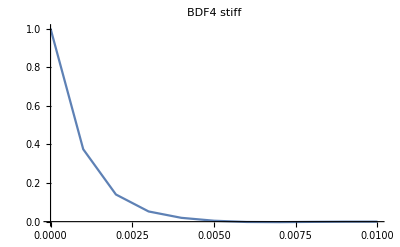

```mathematica
sol = SolveInitialValueProblem[Function[{t,y}, -1000 y], {t, 0., 0.01}, 1.,
  Method -> "BDF4", StepSize -> 0.001];
ListLinePlot[Transpose[{sol["Grid"], sol["Solution"]}], PlotLabel -> "BDF4 stiff"]
```

System ODE: harmonic oscillator {y1'=y2, y2'=-y1}:

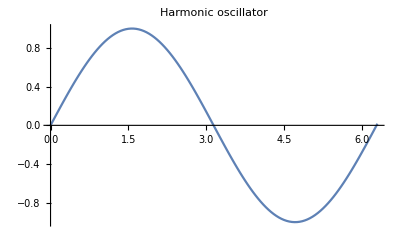

```mathematica
osc = Function[{t, y}, {y[[2]], -y[[1]]}];
sol = SolveInitialValueProblem[osc, {t, 0., 2 Pi}, {0., 1.},
  Method -> "RungeKutta4", StepSize -> 0.05];
ListLinePlot[{Transpose[{sol["Grid"], sol["Solution"][[All,1]]}]},
  PlotLabel -> "Harmonic oscillator"]
```

Complex-valued ODE: i y' = y, y(0)=1 -> e^{-it}:

```mathematica
solZ = SolveInitialValueProblem[Function[{t,z}, -I z], {t, 0., 2 Pi}, 1.+0.I,
  Method -> "RungeKutta4", StepSize -> 0.05];
{Abs[Last[solZ["Solution"]]], Re[solZ["Solution"][[1]]]}  (* |y|=1, y(0)=1 *)
```

{1.,1.}

Compiled option for numeric speed-up:

```mathematica
SolveInitialValueProblem[Function[{t,y},-y], {t,0.,10.}, 1.,
  Method -> "RungeKutta4", StepSize -> 0.001, Compiled -> True]
```

<|Grid→{0.,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,9969,9.985,9.986,9.987,9.988,9.989,9.99,9.991,9.992,9.993,9.994,9.995,9.996,9.997,9.998,9.999,10.},Solution→{1}|>
 |  |  |  |

## Boundary Value Problems

### y'' = -y, y(0)=0, y(Pi)=0; exact: sin(x):

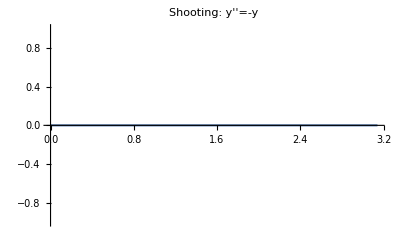

```mathematica
bvpF = Function[{x, y, dy}, -y];
sol = SolveBoundaryValueProblem[bvpF, {x, 0., Pi}, {0., 0.}, 100,
  Method -> "Shooting"];
ListLinePlot[Transpose[{sol["Grid"], sol["Solution"]}],
  PlotLabel -> "Shooting: y''=-y"]
```

```mathematica
sol = SolveBoundaryValueProblem[bvpF, {x, 0., Pi}, {0., 0.}, 100,
  Method -> "FiniteDifference"];
Max[Abs[sol["Solution"] - Sin /@ sol["Grid"]]]  (* max error vs exact *)
```

0.999879

## PDE Numerical Solutions

### SolveParabolicPDE -- heat equation u_t = alpha^2 u_xx

```mathematica
ic = Function[x, Sin[Pi x]]; bc = {Function[t, 0.], Function[t, 0.]};
```

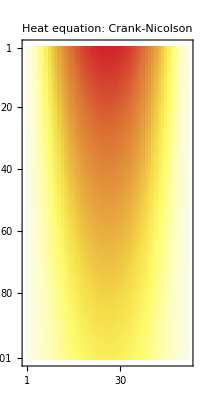

```mathematica
u1 = SolveParabolicPDE[1., {x, 0., 1., 49}, {t, 0., 0.1, 100}, ic, bc,
  Method -> "CrankNicolson"];
MatrixPlot[u1["Solution"], ColorFunction -> "TemperatureMap",
  PlotLabel -> "Heat equation: Crank-Nicolson"]
```

```mathematica
SolveParabolicPDE[1., {x, 0., 1., 49}, {t, 0., 0.05, 50}, ic, bc,
  Method -> "ForwardDifference"];
```

SolveParabolicPDE::stiff: Stability parameter r = 2.5 > 0.5. ForwardDifference may be unstable.

```mathematica
SolveParabolicPDE[1., {x, 0., 1., 49}, {t, 0., 0.05, 50}, ic, bc,
  Method -> "BackwardDifference"];
```

```mathematica
%9
```

<|SpatialGrid→{0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.},TimeGrid→{0.,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05},Solution→{{0.,0.0627905,0.125333,0.187381,0.24869,0.309017,0.368125,0.425779,0.481754,0.535827,0.587785,0.637424,0.684547,0.728969,0.770513,0.809017,0.844328,0.876307,0.904827,0.929776,0.951057,0.968583,0.982287,0.992115,0.998027,1.,0.998027,0.992115,0.982287,0.968583,0.951057,0.929776,0.904827,0.876307,0.844328,0.809017,0.770513,0.728969,0.684547,0.637424,0.587785,0.535827,0.481754,0.425779,0.368125,0.309017,0.24869,0.187381,0.125333,0.0627905,1.22465×10^-16},{0.,0.0621771,0.124109,0.185551,0.24626,0.305998,0.364528,0.421619,0.477047,0.530592,0.582043,0.631196,0.677859,0.721847,0.762985,0.801113,0.836079,0.867745,0.895987,0.920693,0.941765,0.95912,0.97269,0.982422,0.988276,0.99023,0.988276,0.982422,0.97269,0.95912,0.941765,0.920693,0.895987,0.867745,0.836079,0.801113,0.762985,0.721847,0.677859,0.631196,0.582043,0.530592,0.477047,0.421619,0.364528,0.305998,0.24626,0.185551,0.124109,0.0621771,0.},{0.,0.0615696,0.122896,0.183738,0.243854,0.303008,0.360967,0.4175,0.472386,0.525408,0.576356,0.62503,0.671236,0.714794,0.755531,0.793286,0.82791,0.859267,0.887233,0.911697,0.932564,0.94975,0.963187,0.972824,0.978621,0.980556,0.978621,0.972824,0.963187,0.94975,0.932564,0.911697,0.887233,0.859267,0.82791,0.793286,0.755531,0.714794,0.671236,0.62503,0.576356,0.525408,0.472386,0.4175,0.360967,0.303008,0.243854,0.183738,0.122896,0.0615696,0.},{0.,0.0609681,0.121696,0.181943,0.241472,0.300048,0.35744,0.413421,0.467771,0.520275,0.570725,0.618923,0.664678,0.707811,0.74815,0.785536,0.819822,0.850872,0.878565,0.90279,0.923453,0.940471,0.953777,0.963319,0.96906,0.970976,0.96906,0.963319,0.953777,0.940471,0.923453,0.90279,0.878565,0.850872,0.819822,0.785536,0.74815,0.707811,0.664678,0.618923,0.570725,0.520275,0.467771,0.413421,0.35744,0.300048,0.241472,0.181943,0.121696,0.0609681,0.},{0.,0.0603724,0.120507,0.180165,0.239113,0.297116,0.353948,0.409382,0.463201,0.515192,0.565149,0.612876,0.658185,0.700895,0.74084,0.777861,0.811812,0.842559,0.869981,0.89397,0.914431,0.931282,0.944459,0.953908,0.959592,0.961489,0.959592,0.953908,0.944459,0.931282,0.914431,0.89397,0.869981,0.842559,0.811812,0.777861,0.74084,0.700895,0.658185,0.612876,0.565149,0.515192,0.463201,0.409382,0.353948,0.297116,0.239113,0.180165,0.120507,0.0603724,0.},{0.,0.0597826,0.119329,0.178405,0.236777,0.294214,0.35049,0.405383,0.458675,0.510158,0.559628,0.606888,0.651754,0.694048,0.733602,0.770261,0.803881,0.834328,0.861482,0.885236,0.905497,0.922184,0.935231,0.944588,0.950217,0.952095,0.950217,0.944588,0.935231,0.922184,0.905497,0.885236,0.861482,0.834328,0.803881,0.770261,0.733602,0.694048,0.651754,0.606888,0.559628,0.510158,0.458675,0.405383,0.35049,0.294214,0.236777,0.178405,0.119329,0.0597826,0.},{0.,0.0591985,0.118163,0.176662,0.234463,0.291339,0.347065,0.401422,0.454194,0.505174,0.55416,0.600959,0.645387,0.687267,0.726435,0.762736,0.796027,0.826176,0.853065,0.876587,0.89665,0.913174,0.926094,0.935359,0.940933,0.942793,0.940933,0.935359,0.926094,0.913174,0.89665,0.876587,0.853065,0.826176,0.796027,0.762736,0.726435,0.687267,0.645387,0.600959,0.55416,0.505174,0.454194,0.401422,0.347065,0.291339,0.234463,0.176662,0.118163,0.0591985,0.},{0.,0.0586201,0.117009,0.174936,0.232173,0.288493,0.343675,0.3975,0.449757,0.500238,0.548746,0.595088,0.639081,0.680552,0.719338,0.755284,0.78825,0.818105,0.844731,0.868023,0.88789,0.904252,0.917046,0.926221,0.93174,0.933582,0.93174,0.926221,0.917046,0.904252,0.88789,0.868023,0.844731,0.818105,0.78825,0.755284,0.719338,0.680552,0.639081,0.595088,0.548746,0.500238,0.449757,0.3975,0.343675,0.288493,0.232173,0.174936,0.117009,0.0586201,0.},{0.,0.0580474,0.115866,0.173227,0.229904,0.285674,0.340317,0.393617,0.445363,0.495351,0.543385,0.589274,0.632837,0.673903,0.71231,0.747905,0.780549,0.810112,0.836478,0.859542,0.879215,0.895418,0.908087,0.917172,0.922637,0.924461,0.922637,0.917172,0.908087,0.895418,0.879215,0.859542,0.836478,0.810112,0.780549,0.747905,0.71231,0.673903,0.632837,0.589274,0.543385,0.495351,0.445363,0.393617,0.340317,0.285674,0.229904,0.173227,0.115866,0.0580474,0.},{0.,0.0574803,0.114734,0.171534,0.227658,0.282883,0.336992,0.389771,0.441011,0.490512,0.538076,0.583517,0.626655,0.667319,0.70535,0.740598,0.772923,0.802197,0.828305,0.851145,0.870625,0.88667,0.899215,0.908211,0.913623,0.915429,0.913623,0.908211,0.899215,0.88667,0.870625,0.851145,0.828305,0.802197,0.772923,0.740598,0.70535,0.667319,0.626655,0.583517,0.538076,0.490512,0.441011,0.389771,0.336992,0.282883,0.227658,0.171534,0.114734,0.0574803,0.},{0.,0.0569187,0.113613,0.169858,0.225434,0.280119,0.3337,0.385963,0.436703,0.485719,0.532819,0.577816,0.620532,0.6608,0.698459,0.733362,0.765371,0.794359,0.820213,0.842829,0.862119,0.878007,0.890429,0.899338,0.904697,0.906486,0.904697,0.899338,0.890429,0.878007,0.862119,0.842829,0.820213,0.794359,0.765371,0.733362,0.698459,0.6608,0.620532,0.577816,0.532819,0.485719,0.436703,0.385963,0.3337,0.280119,0.225434,0.169858,0.113613,0.0569187,0.},{0.,0.0563626,0.112503,0.168199,0.223231,0.277383,0.330439,0.382192,0.432436,0.480974,0.527613,0.57217,0.61447,0.654344,0.691635,0.726197,0.757894,0.786599,0.812199,0.834595,0.853696,0.869429,0.88173,0.890551,0.895858,0.897629,0.895858,0.890551,0.88173,0.869429,0.853696,0.834595,0.812199,0.786599,0.757894,0.726197,0.691635,0.654344,0.61447,0.57217,0.527613,0.480974,0.432436,0.382192,0.330439,0.277383,0.223231,0.168199,0.112503,0.0563626,0.},{0.,0.055812,0.111404,0.166556,0.22105,0.274673,0.327211,0.378458,0.428211,0.476275,0.522459,0.56658,0.608466,0.647951,0.684878,0.719102,0.750489,0.778914,0.804264,0.826441,0.845356,0.860934,0.873115,0.881851,0.887106,0.88886,0.887106,0.881851,0.873115,0.860934,0.845356,0.826441,0.804264,0.778914,0.750489,0.719102,0.684878,0.647951,0.608466,0.56658,0.522459,0.476275,0.428211,0.378458,0.327211,0.274673,0.22105,0.166556,0.111404,0.055812,0.},{0.,0.0552667,0.110315,0.164928,0.218891,0.271989,0.324014,0.37476,0.424028,0.471622,0.517354,0.561045,0.602522,0.64162,0.678187,0.712077,0.743157,0.771304,0.796407,0.818366,0.837097,0.852523,0.864585,0.873235,0.878439,0.880175,0.878439,0.873235,0.864585,0.852523,0.837097,0.818366,0.796407,0.771304,0.743157,0.712077,0.678187,0.64162,0.602522,0.561045,0.517354,0.471622,0.424028,0.37476,0.324014,0.271989,0.218891,0.164928,0.110315,0.0552667,0.},{0.,0.0547267,0.109237,0.163317,0.216752,0.269332,0.320849,0.371099,0.419885,0.467014,0.5123,0.555564,0.596635,0.635352,0.671561,0.70512,0.735896,0.763768,0.788626,0.810371,0.828918,0.844194,0.856138,0.864704,0.869856,0.871576,0.869856,0.864704,0.856138,0.844194,0.828918,0.810371,0.788626,0.763768,0.735896,0.70512,0.671561,0.635352,0.596635,0.555564,0.5123,0.467014,0.419885,0.371099,0.320849,0.269332,0.216752,0.163317,0.109237,0.0547267,0.},{0.,0.054192,0.10817,0.161721,0.214635,0.2667,0.317714,0.367473,0.415783,0.462451,0.507294,0.550136,0.590806,0.629144,0.665,0.698231,0.728706,0.756306,0.780921,0.802454,0.82082,0.835946,0.847774,0.856255,0.861358,0.863061,0.861358,0.856255,0.847774,0.835946,0.82082,0.802454,0.780921,0.756306,0.728706,0.698231,0.665,0.629144,0.590806,0.550136,0.507294,0.462451,0.415783,0.367473,0.317714,0.2667,0.214635,0.161721,0.10817,0.054192,0.},{0.,0.0536626,0.107113,0.160141,0.212538,0.264095,0.31461,0.363883,0.411721,0.457933,0.502338,0.544761,0.585034,0.622998,0.658503,0.691409,0.721587,0.748917,0.773291,0.794614,0.8128,0.827779,0.839491,0.84789,0.852942,0.854629,0.852942,0.84789,0.839491,0.827779,0.8128,0.794614,0.773291,0.748917,0.721587,0.691409,0.658503,0.622998,0.585034,0.544761,0.502338,0.457933,0.411721,0.363883,0.31461,0.264095,0.212538,0.160141,0.107113,0.0536626,0.},{0.,0.0531383,0.106067,0.158577,0.210461,0.261515,0.311536,0.360328,0.407698,0.453459,0.49743,0.539439,0.579318,0.616911,0.652069,0.684654,0.714537,0.7416,0.765736,0.78685,0.804859,0.819692,0.831289,0.839606,0.844609,0.846279,0.844609,0.839606,0.831289,0.819692,0.804859,0.78685,0.765736,0.7416,0.714537,0.684654,0.652069,0.616911,0.579318,0.539439,0.49743,0.453459,0.407698,0.360328,0.311536,0.261515,0.210461,0.158577,0.106067,0.0531383,0.},{0.,0.0526191,0.105031,0.157028,0.208405,0.25896,0.308492,0.356808,0.403715,0.449029,0.492571,0.534168,0.573658,0.610884,0.645699,0.677965,0.707556,0.734355,0.758255,0.779163,0.796996,0.811683,0.823168,0.831403,0.836357,0.838011,0.836357,0.831403,0.823168,0.811683,0.796996,0.779163,0.758255,0.734355,0.707556,0.677965,0.645699,0.610884,0.573658,0.534168,0.492571,0.449029,0.403715,0.356808,0.308492,0.25896,0.208405,0.157028,0.105031,0.0526191,0.},{0.,0.0521051,0.104004,0.155493,0.206369,0.25643,0.305478,0.353322,0.399771,0.444642,0.487758,0.52895,0.568053,0.604915,0.63939,0.671341,0.700643,0.72718,0.750847,0.771551,0.789209,0.803753,0.815125,0.82328,0.828186,0.829824,0.828186,0.82328,0.815125,0.803753,0.789209,0.771551,0.750847,0.72718,0.700643,0.671341,0.63939,0.604915,0.568053,0.52895,0.487758,0.444642,0.399771,0.353322,0.305478,0.25643,0.206369,0.155493,0.104004,0.0521051,0.},{0.,0.051596,0.102988,0.153974,0.204353,0.253924,0.302494,0.34987,0.395865,0.440298,0.482993,0.523782,0.562504,0.599005,0.633143,0.664782,0.693798,0.720075,0.743511,0.764013,0.781499,0.795901,0.807161,0.815237,0.820095,0.821716,0.820095,0.815237,0.807161,0.795901,0.781499,0.764013,0.743511,0.720075,0.693798,0.664782,0.633143,0.599005,0.562504,0.523782,0.482993,0.440298,0.395865,0.34987,0.302494,0.253924,0.204353,0.153974,0.102988,0.051596,0.},{0.,0.0510919,0.101982,0.15247,0.202356,0.251443,0.299539,0.346452,0.391997,0.435996,0.478274,0.518664,0.557008,0.593153,0.626958,0.658288,0.68702,0.71304,0.736247,0.756548,0.773863,0.788125,0.799276,0.807272,0.812083,0.813688,0.812083,0.807272,0.799276,0.788125,0.773863,0.756548,0.736247,0.71304,0.68702,0.658288,0.626958,0.593153,0.557008,0.518664,0.478274,0.435996,0.391997,0.346452,0.299539,0.251443,0.202356,0.15247,0.101982,0.0510919,0.},{0.,0.0505927,0.100986,0.15098,0.200379,0.248987,0.296612,0.343067,0.388167,0.431736,0.473601,0.513597,0.551566,0.587358,0.620832,0.651856,0.680307,0.706074,0.729054,0.749157,0.766303,0.780425,0.791467,0.799385,0.804149,0.805738,0.804149,0.799385,0.791467,0.780425,0.766303,0.749157,0.729054,0.706074,0.680307,0.651856,0.620832,0.587358,0.551566,0.513597,0.473601,0.431736,0.388167,0.343067,0.296612,0.248987,0.200379,0.15098,0.100986,0.0505927,0.},{0.,0.0500984,0.0999992,0.149505,0.198421,0.246554,0.293714,0.339715,0.384375,0.427518,0.468974,0.508579,0.546177,0.58162,0.614767,0.645488,0.673661,0.699176,0.721931,0.741837,0.758816,0.7728,0.783734,0.791575,0.796292,0.797866,0.796292,0.791575,0.783734,0.7728,0.758816,0.741837,0.721931,0.699176,0.673661,0.645488,0.614767,0.58162,0.546177,0.508579,0.468974,0.427518,0.384375,0.339715,0.293714,0.246554,0.198421,0.149505,0.0999992,0.0500984,0.},{0.,0.049609,0.0990222,0.148045,0.196483,0.244145,0.290845,0.336396,0.38062,0.423341,0.464392,0.50361,0.540841,0.575937,0.60876,0.639181,0.667079,0.692345,0.714878,0.73459,0.751402,0.76525,0.776077,0.783841,0.788512,0.790071,0.788512,0.783841,0.776077,0.76525,0.751402,0.73459,0.714878,0.692345,0.667079,0.639181,0.60876,0.575937,0.540841,0.50361,0.464392,0.423341,0.38062,0.336396,0.290845,0.244145,0.196483,0.148045,0.0990222,0.049609,0.},{0.,0.0491243,0.0980547,0.146598,0.194563,0.24176,0.288003,0.333109,0.376901,0.419205,0.459855,0.49869,0.535557,0.57031,0.602813,0.632936,0.660562,0.685581,0.707894,0.727413,0.744061,0.757773,0.768495,0.776183,0.780809,0.782352,0.780809,0.776183,0.768495,0.757773,0.744061,0.727413,0.707894,0.685581,0.660562,0.632936,0.602813,0.57031,0.535557,0.49869,0.459855,0.419205,0.376901,0.333109,0.288003,0.24176,0.194563,0.146598,0.0980547,0.0491243,0.},{0.,0.0486444,0.0970968,0.145166,0.192662,0.239398,0.285189,0.329855,0.373219,0.41511,0.455362,0.493818,0.530325,0.564738,0.596923,0.626753,0.654108,0.678882,0.700977,0.720306,0.736792,0.75037,0.760987,0.7686,0.77318,0.774709,0.77318,0.7686,0.760987,0.75037,0.736792,0.720306,0.700977,0.678882,0.654108,0.626753,0.596923,0.564738,0.530325,0.493818,0.455362,0.41511,0.373219,0.329855,0.285189,0.239398,0.192662,0.145166,0.0970968,0.0486444,0.},{0.,0.0481691,0.0961481,0.143748,0.19078,0.237059,0.282403,0.326632,0.369572,0.411054,0.450914,0.488993,0.525143,0.559221,0.591091,0.620629,0.647718,0.67225,0.694129,0.713269,0.729593,0.743039,0.753552,0.761091,0.765626,0.76714,0.765626,0.761091,0.753552,0.743039,0.729593,0.713269,0.694129,0.67225,0.647718,0.620629,0.591091,0.559221,0.525143,0.488993,0.450914,0.411054,0.369572,0.326632,0.282403,0.237059,0.19078,0.143748,0.0961481,0.0481691,0.},{0.,0.0476985,0.0952088,0.142343,0.188916,0.234743,0.279644,0.323441,0.365962,0.407038,0.446508,0.484216,0.520013,0.553757,0.585317,0.614566,0.641389,0.665682,0.687347,0.7063,0.722465,0.735779,0.74619,0.753655,0.758146,0.759645,0.758146,0.753655,0.74619,0.735779,0.722465,0.7063,0.687347,0.665682,0.641389,0.614566,0.585317,0.553757,0.520013,0.484216,0.446508,0.407038,0.365962,0.323441,0.279644,0.234743,0.188916,0.142343,0.0952088,0.0476985,0.},{0.,0.0472325,0.0942786,0.140953,0.18707,0.23245,0.276912,0.320281,0.362386,0.403061,0.442146,0.479485,0.514932,0.548347,0.579598,0.608561,0.635123,0.659178,0.680632,0.6994,0.715407,0.728591,0.738899,0.746292,0.750739,0.752223,0.750739,0.746292,0.738899,0.728591,0.715407,0.6994,0.680632,0.659178,0.635123,0.608561,0.579598,0.548347,0.514932,0.479485,0.442146,0.403061,0.362386,0.320281,0.276912,0.23245,0.18707,0.140953,0.0942786,0.0472325,0.},{0.,0.046771,0.0933575,0.139575,0.185243,0.230179,0.274206,0.317152,0.358846,0.399123,0.437826,0.474801,0.509901,0.54299,0.573935,0.602616,0.628918,0.652738,0.673982,0.692566,0.708417,0.721472,0.73168,0.739001,0.743404,0.744874,0.743404,0.739001,0.73168,0.721472,0.708417,0.692566,0.673982,0.652738,0.628918,0.602616,0.573935,0.54299,0.509901,0.474801,0.437826,0.399123,0.358846,0.317152,0.274206,0.230179,0.185243,0.139575,0.0933575,0.046771,0.},{0.,0.0463141,0.0924454,0.138212,0.183433,0.22793,0.271527,0.314053,0.35534,0.395224,0.433548,0.470162,0.50492,0.537685,0.568328,0.596728,0.622773,0.646361,0.667397,0.6858,0.701496,0.714424,0.724532,0.731781,0.736141,0.737597,0.736141,0.731781,0.724532,0.714424,0.701496,0.6858,0.667397,0.646361,0.622773,0.596728,0.568328,0.537685,0.50492,0.470162,0.433548,0.395224,0.35534,0.314053,0.271527,0.22793,0.183433,0.138212,0.0924454,0.0463141,0.},{0.,0.0458616,0.0915422,0.136862,0.181641,0.225703,0.268875,0.310985,0.351868,0.391363,0.429313,0.465568,0.499987,0.532432,0.562775,0.590898,0.616689,0.640046,0.660877,0.6791,0.694643,0.707444,0.717453,0.724631,0.728949,0.73039,0.728949,0.724631,0.717453,0.707444,0.694643,0.6791,0.660877,0.640046,0.616689,0.590898,0.562775,0.532432,0.499987,0.465568,0.429313,0.391363,0.351868,0.310985,0.268875,0.225703,0.181641,0.136862,0.0915422,0.0458616,0.},{0.,0.0454135,0.0906478,0.135524,0.179866,0.223498,0.266248,0.307947,0.348431,0.387539,0.425118,0.46102,0.495102,0.52723,0.557277,0.585125,0.610664,0.633793,0.65442,0.672465,0.687856,0.700532,0.710444,0.717551,0.721827,0.723255,0.721827,0.717551,0.710444,0.700532,0.687856,0.672465,0.65442,0.633793,0.610664,0.585125,0.557277,0.52723,0.495102,0.46102,0.425118,0.387539,0.348431,0.307947,0.266248,0.223498,0.179866,0.135524,0.0906478,0.0454135,0.},{0.,0.0449698,0.0897622,0.1342,0.178109,0.221314,0.263647,0.304938,0.345026,0.383753,0.420965,0.456516,0.490265,0.522079,0.551833,0.579409,0.604698,0.627601,0.648027,0.665895,0.681136,0.693688,0.703503,0.710541,0.714775,0.716188,0.714775,0.710541,0.703503,0.693688,0.681136,0.665895,0.648027,0.627601,0.604698,0.579409,0.551833,0.522079,0.490265,0.456516,0.420965,0.383753,0.345026,0.304938,0.263647,0.221314,0.178109,0.1342,0.0897622,0.0449698,0.},{0.,0.0445305,0.0888852,0.132889,0.176369,0.219152,0.261071,0.301959,0.341655,0.380004,0.416852,0.452055,0.485475,0.516978,0.546441,0.573748,0.59879,0.621469,0.641695,0.659389,0.674481,0.686911,0.696629,0.703599,0.707792,0.709191,0.707792,0.703599,0.696629,0.686911,0.674481,0.659389,0.641695,0.621469,0.59879,0.573748,0.546441,0.516978,0.485475,0.452055,0.416852,0.380004,0.341655,0.301959,0.261071,0.219152,0.176369,0.132889,0.0888852,0.0445305,0.},{0.,0.0440954,0.0880168,0.131591,0.174646,0.217011,0.25852,0.299009,0.338318,0.376291,0.412779,0.447639,0.480732,0.511927,0.541103,0.568142,0.59294,0.615397,0.635426,0.652947,0.667891,0.6802,0.689823,0.696725,0.700877,0.702262,0.700877,0.696725,0.689823,0.6802,0.667891,0.652947,0.635426,0.615397,0.59294,0.568142,0.541103,0.511927,0.480732,0.447639,0.412779,0.376291,0.338318,0.299009,0.25852,0.217011,0.174646,0.131591,0.0880168,0.0440954,0.},{0.,0.0436646,0.0871569,0.130305,0.172939,0.214891,0.255994,0.296087,0.335012,0.372615,0.408747,0.443266,0.476035,0.506926,0.535816,0.562592,0.587147,0.609385,0.629218,0.646568,0.661366,0.673554,0.683084,0.689918,0.694029,0.695401,0.694029,0.689918,0.683084,0.673554,0.661366,0.646568,0.629218,0.609385,0.587147,0.562592,0.535816,0.506926,0.476035,0.443266,0.408747,0.372615,0.335012,0.296087,0.255994,0.214891,0.172939,0.130305,0.0871569,0.0436646,0.},{0.,0.043238,0.0863054,0.129032,0.17125,0.212791,0.253493,0.293195,0.331739,0.368974,0.404753,0.438935,0.471384,0.501973,0.530581,0.557095,0.58141,0.603431,0.623071,0.640251,0.654904,0.666973,0.67641,0.683177,0.687248,0.688607,0.687248,0.683177,0.67641,0.666973,0.654904,0.640251,0.623071,0.603431,0.58141,0.557095,0.530581,0.501973,0.471384,0.438935,0.404753,0.368974,0.331739,0.293195,0.253493,0.212791,0.17125,0.129032,0.0863054,0.043238,0.},{0.,0.0428156,0.0854622,0.127772,0.169577,0.210712,0.251017,0.29033,0.328498,0.365369,0.400799,0.434646,0.466779,0.497069,0.525397,0.551652,0.57573,0.597536,0.616983,0.633996,0.648506,0.660457,0.669802,0.676503,0.680534,0.68188,0.680534,0.676503,0.669802,0.660457,0.648506,0.633996,0.616983,0.597536,0.57573,0.551652,0.525397,0.497069,0.466779,0.434646,0.400799,0.365369,0.328498,0.29033,0.251017,0.210712,0.169577,0.127772,0.0854622,0.0428156,0.},{0.,0.0423973,0.0846272,0.126523,0.16792,0.208654,0.248564,0.287494,0.325289,0.3618,0.396883,0.4304,0.462218,0.492213,0.520264,0.546263,0.570105,0.591698,0.610955,0.627802,0.64217,0.654004,0.663258,0.669893,0.673885,0.675218,0.673885,0.669893,0.663258,0.654004,0.64217,0.627802,0.610955,0.591698,0.570105,0.546263,0.520264,0.492213,0.462218,0.4304,0.396883,0.3618,0.325289,0.287494,0.248564,0.208654,0.16792,0.126523,0.0846272,0.0423973,0.},{0.,0.0419831,0.0838004,0.125287,0.166279,0.206615,0.246136,0.284685,0.322111,0.358265,0.393005,0.426195,0.457702,0.487404,0.515181,0.540926,0.564535,0.585917,0.604986,0.621668,0.635896,0.647615,0.656778,0.663349,0.667301,0.668621,0.667301,0.663349,0.656778,0.647615,0.635896,0.621668,0.604986,0.585917,0.564535,0.540926,0.515181,0.487404,0.457702,0.426195,0.393005,0.358265,0.322111,0.284685,0.246136,0.206615,0.166279,0.125287,0.0838004,0.0419831,0.},{0.,0.0415729,0.0829817,0.124063,0.164655,0.204597,0.243731,0.281904,0.318964,0.354765,0.389166,0.422031,0.453231,0.482642,0.510148,0.535641,0.55902,0.580193,0.599076,0.615594,0.629684,0.641288,0.650361,0.656868,0.660782,0.662088,0.660782,0.656868,0.650361,0.641288,0.629684,0.615594,0.599076,0.580193,0.55902,0.535641,0.510148,0.482642,0.453231,0.422031,0.389166,0.354765,0.318964,0.281904,0.243731,0.204597,0.164655,0.124063,0.0829817,0.0415729,0.},{0.,0.0411667,0.082171,0.122851,0.163046,0.202598,0.24135,0.279149,0.315847,0.351299,0.385364,0.417908,0.448803,0.477926,0.505164,0.530408,0.553558,0.574524,0.593223,0.60958,0.623532,0.635022,0.644007,0.65045,0.654326,0.65562,0.654326,0.65045,0.644007,0.635022,0.623532,0.60958,0.593223,0.574524,0.553558,0.530408,0.505164,0.477926,0.448803,0.417908,0.385364,0.351299,0.315847,0.279149,0.24135,0.202598,0.163046,0.122851,0.082171,0.0411667,0.},{0.,0.0407645,0.0813682,0.121651,0.161453,0.200618,0.238992,0.276422,0.312761,0.347867,0.381599,0.413825,0.444418,0.473257,0.500228,0.525226,0.54815,0.568911,0.587427,0.603624,0.61744,0.628818,0.637715,0.644095,0.647933,0.649214,0.647933,0.644095,0.637715,0.628818,0.61744,0.603624,0.587427,0.568911,0.54815,0.525226,0.500228,0.473257,0.444418,0.413825,0.381599,0.347867,0.312761,0.276422,0.238992,0.200618,0.161453,0.121651,0.0813682,0.0407645,0.},{0.,0.0403662,0.0805732,0.120462,0.159876,0.198658,0.236657,0.273721,0.309706,0.344468,0.37787,0.409782,0.440076,0.468633,0.495341,0.520094,0.542795,0.563353,0.581688,0.597727,0.611407,0.622675,0.631485,0.637802,0.641603,0.642872,0.641603,0.637802,0.631485,0.622675,0.611407,0.597727,0.581688,0.563353,0.542795,0.520094,0.495341,0.468633,0.440076,0.409782,0.37787,0.344468,0.309706,0.273721,0.236657,0.198658,0.159876,0.120462,0.0805732,0.0403662,0.},{0.,0.0399719,0.079786,0.119285,0.158314,0.196717,0.234345,0.271047,0.30668,0.341102,0.374179,0.405778,0.435776,0.464055,0.490502,0.515013,0.537491,0.557849,0.576005,0.591887,0.605434,0.616591,0.625315,0.631571,0.635335,0.636591,0.635335,0.631571,0.625315,0.616591,0.605434,0.591887,0.576005,0.557849,0.537491,0.515013,0.490502,0.464055,0.435776,0.405778,0.374179,0.341102,0.30668,0.271047,0.234345,0.196717,0.158314,0.119285,0.079786,0.0399719,0.},{0.,0.0395813,0.0790065,0.11812,0.156767,0.194795,0.232055,0.268399,0.303684,0.33777,0.370523,0.401814,0.431519,0.459521,0.485709,0.509981,0.53224,0.552399,0.570377,0.586104,0.599519,0.610567,0.619206,0.625401,0.629127,0.630371,0.629127,0.625401,0.619206,0.610567,0.599519,0.586104,0.570377,0.552399,0.53224,0.509981,0.485709,0.459521,0.431519,0.401814,0.370523,0.33777,0.303684,0.268399,0.232055,0.194795,0.156767,0.11812,0.0790065,0.0395813,0.},{0.,0.0391946,0.0782346,0.116966,0.155235,0.192892,0.229788,0.265777,0.300717,0.33447,0.366903,0.397888,0.427303,0.455031,0.480964,0.504999,0.52704,0.547002,0.564805,0.580378,0.593662,0.604602,0.613156,0.619291,0.622981,0.624213,0.622981,0.619291,0.613156,0.604602,0.593662,0.580378,0.564805,0.547002,0.52704,0.504999,0.480964,0.455031,0.427303,0.397888,0.366903,0.33447,0.300717,0.265777,0.229788,0.192892,0.155235,0.116966,0.0782346,0.0391946,0.},{0.,0.0388117,0.0774702,0.115823,0.153719,0.191008,0.227543,0.26318,0.297779,0.331202,0.363318,0.394001,0.423128,0.450586,0.476265,0.500065,0.521891,0.541658,0.559286,0.574708,0.587861,0.598695,0.607166,0.61324,0.616894,0.618114,0.616894,0.61324,0.607166,0.598695,0.587861,0.574708,0.559286,0.541658,0.521891,0.500065,0.476265,0.450586,0.423128,0.394001,0.363318,0.331202,0.297779,0.26318,0.227543,0.191008,0.153719,0.115823,0.0774702,0.0388117,0.},{0.,0.0384325,0.0767134,0.114691,0.152217,0.189142,0.22532,0.260609,0.294869,0.327966,0.359769,0.390151,0.418994,0.446184,0.471612,0.495179,0.516792,0.536366,0.553822,0.569093,0.582118,0.592846,0.601234,0.607249,0.610867,0.612075,0.610867,0.607249,0.601234,0.592846,0.582118,0.569093,0.553822,0.536366,0.516792,0.495179,0.471612,0.446184,0.418994,0.390151,0.359769,0.327966,0.294869,0.260609,0.22532,0.189142,0.152217,0.114691,0.0767134,0.0384325,0.}}|>

### SolveHyperbolicPDE -- wave equation u_tt = c^2 u_xx

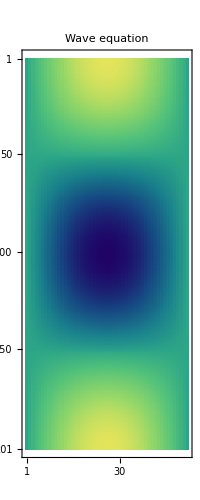

```mathematica
uw = SolveHyperbolicPDE[1., {x, 0., 1., 49}, {t, 0., 2., 200},
  Function[x, Sin[Pi x]], Function[x, 0.],
  {Function[t, 0.], Function[t, 0.]}];
MatrixPlot[uw["Solution"], ColorFunction -> "BlueGreenYellow",
  PlotLabel -> "Wave equation"]
```

### SolveEllipticPDE -- Poisson equation nabla^2 u = f(x,y)

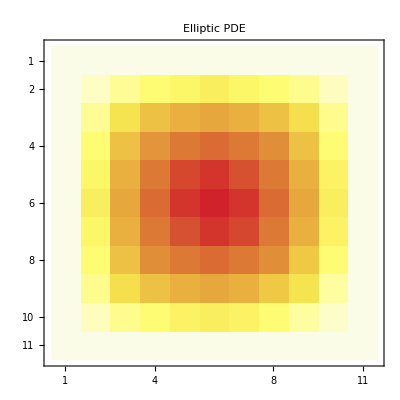

```mathematica
uE = SolveEllipticPDE[Function[{x, y}, -2.],
  {x, 0., 1., 9}, {y, 0., 1., 9},
  {Function[y, 0.], Function[y, 0.], Function[x, 0.], Function[x, 0.]}];
MatrixPlot[uE["Solution"], ColorFunction -> "TemperatureMap",
  PlotLabel -> "Elliptic PDE"]
```

### SolveParabolicPDE2D -- 2D heat equation via ADI

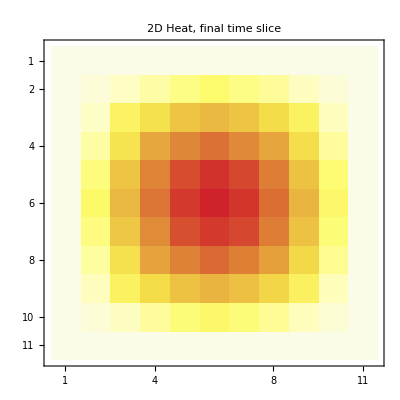

```mathematica
uP2 = SolveParabolicPDE2D[1.,
  {x, 0., 1., 9}, {y, 0., 1., 9}, {t, 0., 0.01, 10},
  Function[{x, y}, Sin[Pi x] Sin[Pi y]],
  {Function[y, 0.], Function[y, 0.], Function[x, 0.], Function[x, 0.]}];
MatrixPlot[uP2["Solution"][[-1]], ColorFunction -> "TemperatureMap",
  PlotLabel -> "2D Heat, final time slice"]
```

### SolveHyperbolicPDE2D -- 2D wave equation (explicit difference)

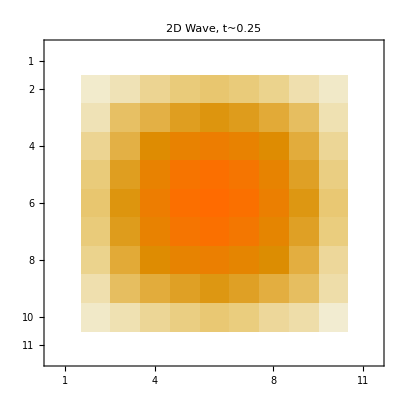

```mathematica
uw2 = SolveHyperbolicPDE2D[1.,
  {x, 0., 1., 9}, {y, 0., 1., 9}, {t, 0., 0.5, 50},
  Function[{x,y}, Sin[Pi x] Sin[Pi y]], Function[{x,y}, 0.],
  {Function[y, 0.], Function[y, 0.], Function[x, 0.], Function[x, 0.]}];
MatrixPlot[uw2["Solution"][[25]], PlotLabel -> "2D Wave, t~0.25"]
```

## Linear Equation Systems

### SolveLinearEquationSystem -- ten methods

```mathematica
A = {{4.,2.,1.},{2.,5.,3.},{1.,3.,6.}}; b = {1.,2.,3.};
```

Direct methods:

```mathematica
SolveLinearEquationSystem[A, b, Method -> "GaussianEliminationPivot"]
```

{0.0895522,0.104478,0.432836}

```mathematica
SolveLinearEquationSystem[A, b, Method -> "GaussianElimination"]
```

{0.0895522,0.104478,0.432836}

```mathematica
SolveLinearEquationSystem[A, b, Method -> "GaussJordan"]
```

{0.0895522,0.104478,0.432836}

```mathematica
SolveLinearEquationSystem[A, b, Method -> "LU"]
```

{0.0895522,0.104478,0.432836}

```mathematica
SolveLinearEquationSystem[A, b, Method -> "Cholesky"]
```

{0.0895522,0.104478,0.432836}

```mathematica
SolveLinearEquationSystem[A, b, Method -> "LDLT"]
```

{0.0895522,0.104478,0.432836}

```mathematica
With[{T = {{4.,-1.,0.},{-1.,4.,-1.},{0.,-1.,4.}}},
  SolveLinearEquationSystem[T, {1.,1.,1.}, Method -> "Tridiagonal"]]
```

{0.357143,0.428571,0.357143}

Iterative methods:

```mathematica
SolveLinearEquationSystem[A, b, Method -> "Jacobi"]
```

{0.0895522,0.104478,0.432836}

```mathematica
SolveLinearEquationSystem[A, b, Method -> "GaussSeidel"]
```

{0.0895522,0.104478,0.432836}

```mathematica
SolveLinearEquationSystem[A, b, Method -> "SOR", Omega -> 1.3]
```

{0.0895522,0.104478,0.432836}

Sparse / Krylov methods:

```mathematica
SolveLinearEquationSystem[A, b, Method -> "ConjugateGradient"]
```

{0.0895522,0.104478,0.432836}

Sparse direct (converts A to SparseArray internally):

```mathematica
SolveLinearEquationSystem[SparseArray[A], b, Method -> "SparseDirectLU"]
```

{0.0895522,0.104478,0.432836}

### Matrix decompositions

```mathematica
{L, U, P} = LUDecompose[A];
Norm[P . A - L . U]  (* should be ~0 *)
```

0.

```mathematica
{Q, R} = QRDecompose[A];
{Norm[A - Q.R], Norm[Transpose[Q].Q - IdentityMatrix[3]]}
```

{2.28548×10^-15,3.2858×10^-16}

```mathematica
{Q, R} = QRDecompose[A, Method -> "GramSchmidt"];
Norm[A - Q.R]
```

3.44305

```mathematica
L = CholeskyDecompose[A];
Norm[A - L . Transpose[L]]
```

0.

```mathematica
{Ld, d} = LDLTDecompose[A];
Norm[A - Ld . DiagonalMatrix[d] . Transpose[Ld]]
```

0.

## Matrix Eigenanalysis

```mathematica
M = {{4.,1.,2.},{1.,3.,0.},{2.,0.,5.}};
```

### FindDominantEigenvalue -- largest-modulus eigenvalue:

```mathematica
FindDominantEigenvalue[M, Method -> "PowerMethod"]
```

<|Eigenvalue→6.66908,Eigenvector→{0.631179,0.172027,0.75632},Iterations→30,Converged→True|>

Find eigenvalue nearest to Shift = 3.0:

```mathematica
FindDominantEigenvalue[M, Method -> "InversePowerMethod", Shift -> 3.0]
```

<|Eigenvalue→3.47602,Eigenvector→{0.374362,0.786436,-0.491296},Iterations→25,Converged→True|>

### FindMatrixEigenvalues -- all eigenvalues:

```mathematica
FindMatrixEigenvalues[M, Method -> "JacobiMethod"]  (* symmetric only *)
```

<|Eigenvalues→{3.47607,2.98276,5.54117},Eigenvectors→{{0.368401,0.788138,-0.493071},{-0.289464,0.601253,0.744785},{0.883454,-0.131654,0.44964}},Iterations→501|>

```mathematica
FindMatrixEigenvalues[M, Method -> "QRIteration"]  (* general *)
```

<|Eigenvalues→{6.66908,1.8549,3.47602},Eigenvectors→{{0.631179,-0.753406,0.184371},{0.679313,0.651678,0.337416},{-0.374362,-0.087724,0.923124}},Iterations→30|>

Verify: eigenvalue sum = trace:

```mathematica
Total[FindMatrixEigenvalues[M]["Eigenvalues"]] - Tr[M]
```

-7.10543×10^-15

## Polynomial Interpolation

```mathematica
xs = Range[0., 5.]*1.; ys = Sin /@ xs;
```

### PolynomialInterpolate:

```mathematica
PolynomialInterpolate[xs, ys, 1.5, Method -> "Newton"]
```

1.00161

```mathematica
PolynomialInterpolate[xs, ys, 1.5, Method -> "Lagrange"]
```

1.00161

Compare both methods at 20 query points:

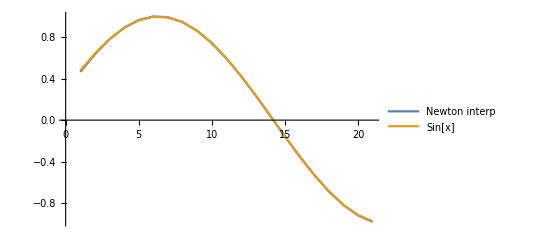

```mathematica
qpts = Range[0.5, 4.5, 0.2];
ListLinePlot[{
  PolynomialInterpolate[xs, ys, #] & /@ qpts,
  Sin /@ qpts},
  PlotLegends -> {"Newton interp", "Sin[x]"}]
```

### HermiteInterpolate -- matches values and derivatives:

```mathematica
xs3 = {0., Pi/2, Pi};
HermiteInterpolate[xs3, Sin /@ xs3, Cos /@ xs3, Pi/4]  (* ~ Sin[Pi/4] *)
```

0.709762

### SplineInterpolate -- three degree options:

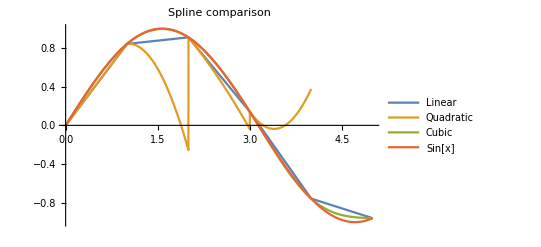

```mathematica
Plot[{
  SplineInterpolate[xs, ys, x, Degree -> 1],
  SplineInterpolate[xs, ys, x, Degree -> 2],
  SplineInterpolate[xs, ys, x, Degree -> 3],
  Sin[x]},
  {x, 0., 5.},
  PlotLegends -> {"Linear", "Quadratic", "Cubic", "Sin[x]"},
  PlotLabel -> "Spline comparison"]
```

## Polynomial Approximation

### ChebyshevApproximate -- Chebyshev expansion:

```mathematica
fCheb = ChebyshevApproximate[Exp, {x, 0., 2.}, 10];
```

```mathematica
fCheb[1.5]  (* ~ Exp[1.5] *)
```

4.48169

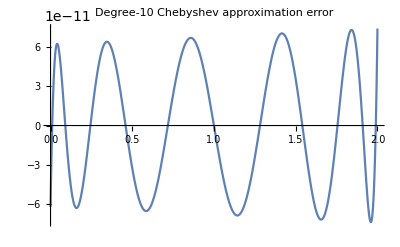

```mathematica
Plot[{Exp[x] - fCheb[x]}, {x, 0., 2.},
  PlotLabel -> "Degree-10 Chebyshev approximation error"]
```

Accuracy improves exponentially with degree:

```mathematica
Table[{n, Max[Abs[ChebyshevApproximate[Exp, {x,0.,2.}, n][#] - Exp[#] &/@ Range[0.,2.,0.1]]]},
  {n, {4, 6, 8, 12}}]
```

{{4,0.00173888},{6,9.84042×10^-6},{8,3.31361×10^-8},{12,5.93747×10^-13}}

### LeastSquaresApproximate -- discrete fitting:

```mathematica
xs5 = Range[-2., 2., 0.5];
ys5 = 2 + 3 # - #^2 & /@ xs5;
basis = {Function[x, 1.], Function[x, x], Function[x, x^2]};
LeastSquaresApproximate[xs5, ys5, basis]  (* should give ~{2,3,-1} *)
```

{2.,3.,-1.}

QR-based variant (more stable for ill-conditioned data):

```mathematica
LeastSquaresApproximate[xs5, ys5, basis, "Orthogonal"]
```

{2.,3.,-1.}

### PadeApproximate -- rational approximant [p/q]:

```mathematica
R = PadeApproximate[Exp, 0., {3, 3}];
```

```mathematica
Table[{x, Exp[x], R[x], Abs[Exp[x]-R[x]]}, {x,-1.,1.,0.25}]
```

### RemezApproximate -- minimax polynomial:

```mathematica
res = RemezApproximate[Sin, {0., Pi}, 5];
```

```mathematica
res["Error"]  (* minimax error E* *)
```

```mathematica
Length[res["Nodes"]]  (* should be degree+2 = 7 equioscillation nodes *)
```

### ScatteredInterpolate -- 2D scattered data:

```mathematica
SeedRandom[7];
```

```mathematica
pts  = RandomReal[{0.,1.}, {30,2}];
vals = Sin[Pi #[[1]]] Cos[Pi #[[2]]] & /@ pts;
```

Thin plate spline (default -- global, C2 smooth):

```mathematica
ScatteredInterpolate[pts, vals, {0.5, 0.5}]  (* ~ Sin[Pi/2]*Cos[Pi/2] = 0 *)
```

Inverse distance weighting:

```mathematica
ScatteredInterpolate[pts, vals, {0.5, 0.5}, Method -> "InverseDistance"]
```

Nearest neighbour:

```mathematica
ScatteredInterpolate[pts, vals, {0.5, 0.5}, Method -> "NearestNeighbor"]
```

Batch evaluation at a grid of query points:

```mathematica
qGrid = Flatten[Table[{x,y}, {x,0.1,0.9,0.1},{y,0.1,0.9,0.1}], 1];
gridVals = ScatteredInterpolate[pts, vals, qGrid];
Length[gridVals]
```